```mathematica
U = 1/4 x^4+ 1/3 x^3 - 3x^2
k = -4
u = 3
SOL = U /.x -> k
Z[x_,y_] := 1/2y^2 + 1/4 x^4+ 1/3 x^3 - 3x^2
```

-3 x^2+x^3/3+x^4/4

-4

3

-16/3

```mathematica
Z[k,u]
```

-5/6

5

ⅇ^(-5/2 (-1+x)^2) (5/π)^(1/4)

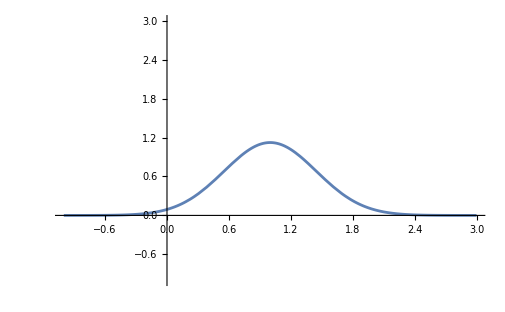

```mathematica
a= 5
f= Exp[-a/2(x-1)^2](a/Pi)^(1/4)
Plot[f,{x,-1,3},PlotRange->{-1,3}]
```

6.58×10^-16

Sin[5 p]/(p √(5 π))

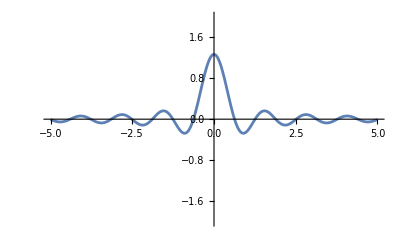

```mathematica
h = 6.58*10^(-16)
g = Sqrt[a/(Pi)]*Sin[(p*a)]/(p*a)
Plot[g,{p,-5,5},PlotRange -> {-2,2}]
```

```mathematica
k0 = 1
```

1

5

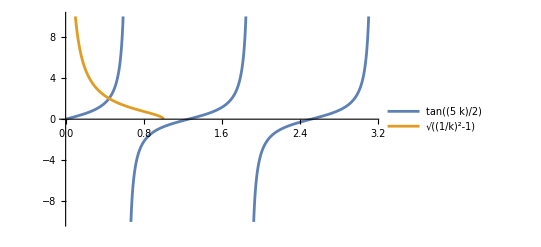

```mathematica
a = 5
p1 =Plot[{Tan[a/2k],Sqrt[(k0/k)^2 - 1]},{k,0,Pi},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

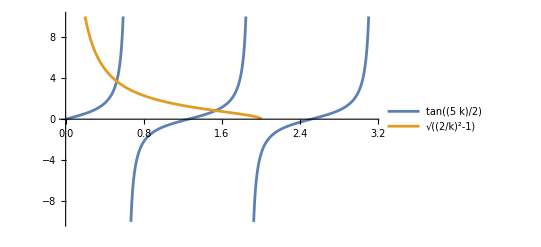

```mathematica
p2 =Plot[{Tan[a/2k],Sqrt[(2/k)^2 - 1]},{k,0,Pi},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

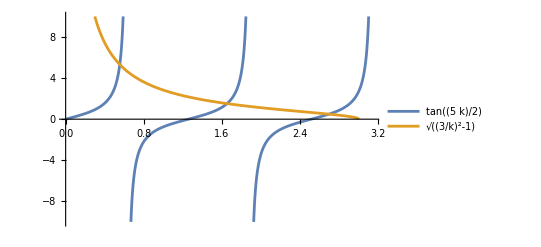

```mathematica
p5=Plot[{Tan[a/2k],Sqrt[(3/k)^2 - 1]},{k,0,Pi},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

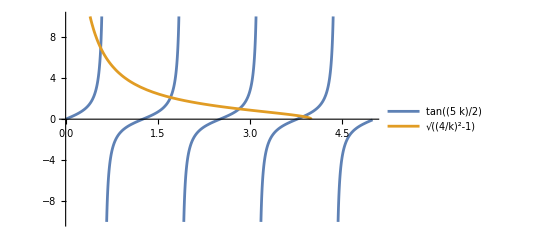

```mathematica
p4 =Plot[{Tan[a/2k],Sqrt[(4/k)^2 - 1]},{k,0,5},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

```mathematica
GraphicsGrid[{{p1,p2},{p5,p4}}]
```

-Graphics-

```mathematica
q = 1.6*10^(-19)
d = 8.8*10^(-12)

a[x_,y_] := q/(4*3.14*d)*(x/Sqrt[(x)^2 + (y)^2])
```

1.6×10^-19

8.8×10^-12

SetDelayed::write: Tag Integer in 5[x_,y_] is Protected.

$Failed